# Pentagons

In this notebook, we figure out the basics of drawing shapes in mathematica and automating replacement rules

## Drawing pentagons

```mathematica
l
```

Line[{{0,0},{1,0}}]

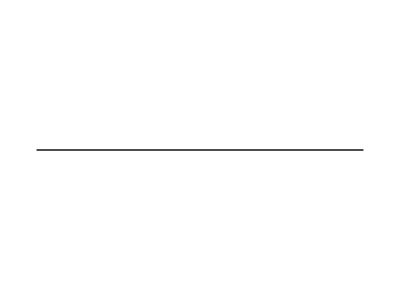

```mathematica
Graphics[l=Line[{{0,0},{1,0}}]]
```

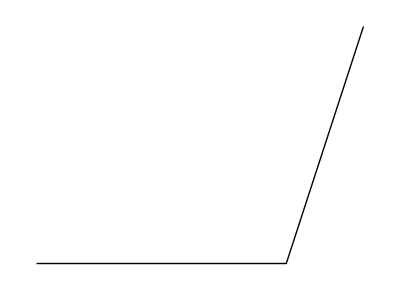

```mathematica
NextCoords[coords1_,coords2_,angle_]:=Module[
{coords3},
coords3 = 2*coords2 - coords1;
RotationTransform[angle,coords2][coords3] //N (*comment N out to keep maximum precision*)
]

point1 = {0,0}; point2={1,0};
Graphics[Line[{point1,point2,NextCoords[point1,point2,Pi-3Pi/5]}]]
```

```mathematica
Pentagon[coords1_,coords2_]:=Module[
{i,l={coords1,coords2}},
For[i=0, i<3, i++,
AppendTo[l,NextCoords[l⟦-2⟧,l⟦-1⟧,2Pi/5]];
];Append[l,coords1]
]
```

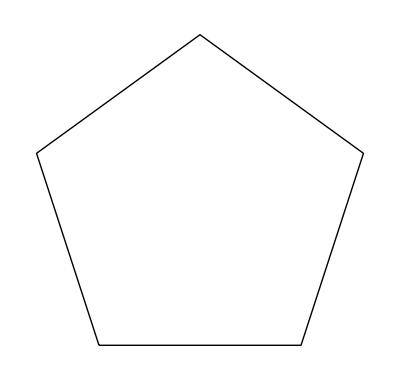

```mathematica
point1 = {0,0}; point2={1,0};
Graphics[Line[Pentagon[point1,point2]]]
```

## Replacing smaller pentagons

We get a new pentagon at vertex, plus one at the centre

```mathematica
point1 = {0,0}; point2={1,0};
startPentagon = Pentagon[point1,point2]
```

{{0,0},{1,0},{1.30902,0.951057},{0.5,1.53884},{-0.309017,0.951057},{0,0}}

```mathematica
makePentagons[startPentagon_]:=Module[
{i, coords1, coords2,scale = 1/(GoldenRatio+1) //N,l={startPentagon}},
(*The vertex pentagons*)
For[i=1,i<6,i++,
{coords1,coords2} = startPentagon⟦i;;i+1⟧;
coords2 = coords1 + scale(coords2-coords1);
AppendTo[l, Pentagon[coords1,coords2]];
];
(*The centre pentagon*)
{coords1,coords2} = {l⟦-1⟧⟦4⟧, l⟦-1⟧⟦3⟧};
Append[l, pentagon[coords1,coords2]][[2;;]]
]
```

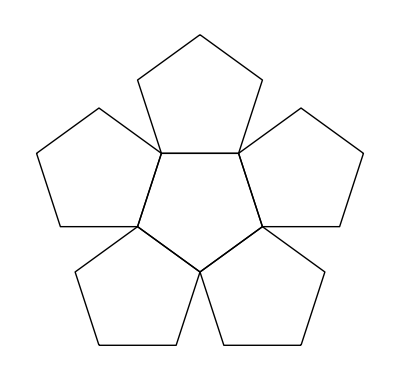

```mathematica
point1 = {0,0}; point2={1,0};
startPentagon = Pentagon[point1,point2];
Graphics[Line/@ makePentagons[startPentagon]]
```

```mathematica
point1 = {0,0}; point2={1,0};
startPentagon = Pentagon[point1,point2];
makePentagons[startPentagon][[1]]
```

{{0,0},{0.381966,0.},{0.5,0.363271},{0.190983,0.587785},{-0.118034,0.363271},{0,0}}

```mathematica
Important: need always a list of pentagons at each operation, not a list of list of lists etc
```

```mathematica
Iterate[pentagonList_]:=
Flatten[makePentagons/@pentagonList,1]
```

```mathematica
Graphics[Line /@Iterate[{startPentagon}]]
```

-Graphics-

```mathematica
Graphics[Line /@Iterate[makePentagons[startPentagon]]]
```

```mathematica
Dimensions[%158]
```

{6,6,6,2}

```mathematica
Module[{imax = 4, list },
list=NestList[Iterate,{startPentagon},imax];
Manipulate[
Graphics[Line/@list[[i]]]
,{i,1,imax,1}
]
]
```